CITE THIS NOTEBOOK: The fragility of an incomplete monetary union by Jamel Saadaoui. Wolfram Community MAR 4 2023.

In this blog, I will show how to build a model of the fragility of an incomplete monetary union. The idea is to find the optimal inflation rule and to examine different configurations for fixed exchange rate and expectation of a devaluation. To this end, I will use Mathematica and the chapter 5 of this book ( https://global.oup.com/ushe/product/economics-of-the-monetary-union-9780198849544 ), that I use in my lecture of Economics of Monetary Union. Allow me to explain the different steps in the notebook below. I would like to publicly thank Paul De Grauwe for providing his very clear lecture notes.

### The model

```mathematica
ClearAll["Global`*"] (*completely clear global symbols to start fresh*)
```

The Phillips curve:

U=U_N+a(π^e−π)+ε

```mathematica
U=UN+a(pe-p)+ϵ
```

a (-p+pe)+UN+ϵ

Alternatively, you can specify the supply curve

Y=Y_n+θ(π−π^e)+ε

Loss function of authorities

L=π^2+β(U−U^-)^2

```mathematica
L=p^2+β(U-UB)^2
```

p^2+β (a (-p+pe)-UB+UN+ϵ)^2

with UB = target unemployment

U^-=λ U_N

```mathematica
UB=λUN
```

λUN

where λ < 1

p^2+β (a (-p+pe)+UN+ϵ-λUN)^2

```mathematica
p^2+β (a (-p+pe)+UN+ϵ-λUN)^2
```

p^2+β (a (-p+pe)+UN+ϵ-λUN)^2

L=π^2+β[(1−λ)U_N+a(π^e−π)+ε]^2

Workers set wages based on pe

Authorities minimize loss given these expectations

Note : authorities directly control inflation

Authorities minimize loss given these expectations

dL/dπ=2π+2β(−a)[(1−λ)U_N+a(π^e−π)+ε]=0

```mathematica
CBLoss=D[L,p]
```

2 p-2 a β (a (-p+pe)+UN+ϵ-λUN)

```mathematica
CBLoss1 = Simplify[Collect[CBLoss, βa]/2]
```

p-a β (a (-p+pe)+UN+ϵ-λUN)

```mathematica
Collect[CBLoss1,p]
```

-a^2 pe β-a UN β+p (1+a^2 β)-a β ϵ+a β λUN

π(1+β a^2)−βa(1−λ)U_N−β a^2 π^e−βaε=0

π(1+β a^2)−βa(1−λ)U_N−β a^2 π^e−βaε=0

```mathematica
p(1+βa^2)-βa(1-λ)UN-βa^2pe-βaϵ==0
```

-pe βa^2+p (1+βa^2)-βaϵ-UN βa (1-λ)==0

```mathematica
Solve[-pe βa^2+p (1+βa^2)-UN βa (1-λ)-βaϵ==0,p]
```

{{p→(UN βa+pe βa^2+βaϵ-UN βa λ)/(1+βa^2)}}

π=(βa(1−λ)U_N)/(1+β a^2)+(β a^2 π^e)/(1+β a^2)+βaε/(1+β a^2)

This is optimal policy rule of authorities given expectations
Agents know this rule
Thus when forming expectations pe they use this rule

π=(βa(1−λ)U_N)/(1+β a^2)+(β a^2 π^e)/(1+β a^2)+βaε/(1+β a^2)

```mathematica
p=(βa(1- λ)UN+pe βa^2+βaϵ)/(1+βa^2)
```

(pe βa^2+βaϵ+UN βa (1-λ))/(1+βa^2)

Set  p = pe and assume first no shocks (ϵ = 0)

π=(βa(1−λ)U_N)/(1+β a^2)+(β a^2 π^e)/(1+β a^2)+βaε/(1+β a^2)

π^e=(βa(1−λ)U_N)/(1+β a^2)+(β a^2 π^e)/(1+β a^2)

```mathematica
Solve[(βa(1- λ)UN+pe βa^2)/(1+βa^2)-pe==0,pe]
```

{{pe→-UN βa (-1+λ)}}

π=π^e=βa(1−λ)U_N

```mathematica
(*there is an inflation bias (non-zero inflation), which increases with β,a.*)
```

When shocks (e . g ., deterioration of trade balance) occur, solution is

π=π^e+βa/(1+β a^2)ε=βa(1−λ)U_N+βa/(1+β a^2)ε

Authorities react to shocks in a stabilizing manner depending on β

if β = 0: no stabilization (strict inflation targeting)

if β > 0: some stabilization

Substitute optimal inflation π^e-π in Phillips curve

```mathematica
UN+a(-βa/(1+βa^2)ϵ)+ϵ
```

UN+ϵ-(a βa ϵ)/(1+βa^2)

```mathematica
Together[UN+ϵ-(a βa ϵ)/(1+βa^2)]
```

(UN+UN βa^2+ϵ-a βa ϵ+βa^2 ϵ)/(1+βa^2)

```mathematica
FullSimplify[(UN+UN βa^2+ϵ-a βa ϵ+βa^2 ϵ)/(1+βa^2)]
```

UN+((1-a βa+βa^2) ϵ)/(1+βa^2)

U=U_N+1/(1+β a^2)ε

If β = 0,
var U = var ϵ : no stabilization.
More generally, Var U = (1/(1+β a^2))^2 var ϵ < 1 depending on β.

Indifference curves between inflation and excess unemployment:

Phillips curve with forward looking expectations:

Credibility of the monetary authority

We use this model to analyze crisis 
Assume PPP : Ṡ=π−π^* set π^*=0
Fixing exchange rate is equivalent to announcing zero inflation
If there is no cost associated to devaluation fixing exchange rate is never credible

Italy will not follow its commitment to the announced FX

If no cost of devaluation, the peg by Italy is not credible and will be attacked

Two countries must have same preferences

Even if they have same preferences, asymmetric shocks may reduce credibility

Italy must now accept too high unemployment to maintain the FX

Italy must now accept too high unemployment

Italian authorities would like Germany to accommodate

If Germany refuses

conflict

loss of credibility

Attack on the system

Case study : EMS during 1992 - 1993

If there is a cost of devaluation, the fixed exchange rate can be made credible

### The model with multiple equilibria

We will compute the loss of the authorities under different expectations of private agents

Loss under discretion

This is the loss when CB follows discretionary policy which is fully expected
This is solution derived earlier

π=π^e=βa(1−λ)U_N

U=U_N

U^-=λ U_N

Substitute into loss function : L=π^2+β(U−U^-)^2

L_DIS=β^2 a^2[(1−λ)U_N]^2+β[U_N(1−λ)]^2

L_DIS=β[(1−λ)U_N]^2(β a^2+1)=βk^2(1+β a^2)

```mathematica
LDIS=βk^2(1+βa^2)
```

(1+βa^2) βk^2

Loss of fixed exchange rate (zero inflation) when agents expect fixed exchange rate

π=π^e=0

U=U_N

L_(0,π^e=0)=β[U_N−U^-]^2=β[(1−λ)U_N]^2=β k^2

```mathematica
LFXZERO=βk^2
```

βk^2

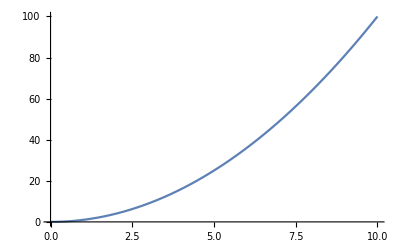

```mathematica
Plot[LFXZERO,{βk,0,10}]
```

Loss when the CB devalues (cheats) while agents expect fixed exchange rate

Take optimal inflation from first order condition and set pe = 0 (also ϵ = 0)

π=(βa(1−λ)U_N)/(1+β a^2)+(β a^2 π^e)/(1+β a^2)+βaε/(1+β a^2)

π=(βa(1−λ)U_N)/(1+β a^2)

U=U_N+a[−(βa(1−λ)U_N)/(1+β a^2)]

Substitute into loss function

```mathematica
(βa(1- λ)UN)/(1+βa^2)
```

(UN βa (1-λ))/(1+βa^2)

```mathematica
UN+a[-(UN βa (1-λ))/(1+βa^2)]
```

UN+a[-(UN βa (1-λ))/(1+βa^2)]

L_cheat=[(βa(1−λ)U_N)/(1+β a^2)]^2+β[(1−λ)U_N−(βa^2(1−λ)U_N)/(1+β a^2)]^2=[(βa(1−λ)U_N)/(1+β a^2)]^2+β[(1−λ)U_N(1−(β a^2)/(1+β a^2))]^2
=[(βa(1−λ)U_N)/(1+β a^2)]^2+β[((1−λ)U_N)/(1+β a^2)]^2=[((1−λ)U_N)/(1+β a^2)]^2 β(β a^2+1)
=β[(1−λ)U_N]^2/(1+β a^2)=(β k^2)/(1+β a^2)

```mathematica
(βa)^2(((1-λ)UN)/(1+βa^2))^2+β(((1-λ)UN)/(1+βa^2))^2
```

(UN^2 β (1-λ)^2)/((1+βa^2)^2)+(UN^2 βa^2 (1-λ)^2)/((1+βa^2)^2)

```mathematica
β(β a^2+1)
```

β[1+a^2 β]

```mathematica
%==(βa)^2+β
```

β[1+a^2 β]==β+βa^2

```mathematica
Equal[%]
```

True

```mathematica
LCHEAT=(β k^2)/(1+β a^2)
```

(k^2 β)/(1+a^2 β)

The difference between LFXZERO and LCHEAT and measures the temptation to devalue

```mathematica
LFXZERO-LCHEAT
```

-(k^2 β)/(1+a^2 β)+βk^2

```mathematica
Together[-(k^2 β)/(1+a^2 β)+βk^2]
```

(-k^2 β+βk^2+a^2 β βk^2)/(1+a^2 β)

L_(0,π^e=0)−L_cheat=β k^2−(β k^2)/(1+β a^2)
=βk^2(1−1/(1+β a^2))
=(β^2 k^2 a^2)/(1+β a^2)>0

Suppose there is a fixed cost of devaluation (e.g. it is costly politically; cf. R. Cooper)
Call this cost C 
Then if C > temptation = (β^2 k^2 a^2)/(1+β a^2) fixed exchange rate is credible

This does not yet mean, however, that it will last

Loss when authorities maintain fixed exchange rate while agents expect devaluation (discretion)

Call this loss under stabilisation

π=0
π^e=βa(1−λ)U_N=βak
U=U_N+a(βa(1−λ)U_N)

L_stab=0+β[U_N+a(βa(1−λ)U_N)−U^-]^2=β[(1−λ)U_N+a^2 β(1−λ)U_N]^2
=β[(1−λ)U_N(1+a^2 β)]^2=β k^2(1+a^2 β)^2

```mathematica
β((1-λ)UN+a^2 β(1-λ)UN)^2
```

β (UN (1-λ)+a^2 UN β (1-λ))^2

```mathematica
Collect[β (UN (1-λ)+a^2 UN β (1-λ))^2,(1+2aβ)]
```

β (UN (1-λ)+a^2 UN β (1-λ))^2

```mathematica
Equal[UN (1-λ)+a^2 UN β (1-λ)==UN (1-λ)(1+a^2 β)]
```

True

```mathematica
LSTAB=βk^2(1+a^2 β)^2
```

(1+a^2 β)^2 βk^2

Comparing LDIS with LSTAB allows us to find the cost of defending the peg

L_stab−L_dis=β k^2(1+a^2 β)^2−βk^2(1+a^2 β)=βk^2(1+a^2 β)a^2 β
=β^2 a^2 k^2(1+a^2 β)>0

```mathematica
LSTAB-LDIS
```

(1+a^2 β)^2 βk^2-(1+βa^2) βk^2

```mathematica
Simplify[(1+a^2 β)^2 βk^2-(1+βa^2) βk^2]
```

(-1+(1+a^2 β)^2-βa^2) βk^2

```mathematica
Equal[(-1+(1+a^2 β)^2-βa^2) βk^2==β k^2(1+β a^2)a^2 β]
```

True

```mathematica
(1+a^2 β)^2
```

(1+a^2 β)^2

```mathematica
Expand[(1+a^2 β)^2]==1+2 a^2 β+(a^2 β*a^2 β)
```

True

Cost of defending when attacked > Temptation when no attack

If C > cost of defense = β^2 a^2 k^2(1+a^2 β) authorities will not yield 
Speculators know this
Therefore they will not attack

### Three possible cases

(β^2 k^2 a^2)/(1+a^2 β)<β^2 k^2 a^2(1+a^2 β)<C

Temptation < cost of defense when attacked < C
	Fixed exchange rate is credible and will not be attacked

C<(β^2 k^2 a^2)/(1+a^2 β)<β^2 k^2 a^2(1+a^2 β)

Fixed exchange rate has no credibility and will be attacked with certainty

(β^2 k^2 a^2)/(1+a^2 β)<C<β^2 k^2 a^2(1+a^2 β)

Two expectations are model consistent:
  	
  	- Agents do not expect a devaluation; 
  	  In that case authorities temptation to devalue is smaller than the cost of devaluation 
  	  So, authorities do not devalue
  	  
  	- Agents expect a devaluation; 
  	  In this case the authorities cost of defending the peg exceeds the cost of devaluation
  	  So, authorities devalue

There are two possible equilibria
Which on will prevail solely depends on expectations which become self - fulfilling

### Importance of weight attached to stabilization (β)

Recall that (a^2 β^2 k^2)/(1+a^2 β): Temptation to devalue
Recall that a^2 β^2 k^2(1+a^2 β) : Cost of defense when attacked

If β = 0 (no desire to stabilize) then C > 0 ensures there is never an attack

With cost of devaluation C_0

⇒ range of β between β_1 and β_2 with multiple equilibria

With β sufficiently ⇒ high always attack

### Two conclusions

1) Too strong ambitions to stabilize make fixed exchange rate regime fragile
    
    2) Making devaluation more costly, improves conditions for survival of fixed exchange rate
    
		- Case study : ERM during 1996 - 1998
        
		- Cost of devaluation was drastically increased (cf. convergence criteria)

## Reference

Economics of the Monetary Union, Thirteenth Edition, 2020, ISBN : 9780198849544, 304 pages
https://global.oup.com/ushe/product/economics-of-the-monetary-union-9780198849544